```mathematica
Needs["PlotLegends`"]
MatrixCutFunction[mat_,{t0_,tf_},{T0_,Tf_},thresh_] := Module[{i,j,nmat},
nmat = mat[[t0;;tf,T0;;Tf]];
For[i = 1, i ≤ Length[nmat],i++,
For[j=1,j≤Length[nmat[[1]]],j++,
nmat[[i,j]] = If[nmat[[i,j]]≤ thresh,1,0];
];
];
Return[nmat];
];
PlotGrids[i_,date_,dir_,datdir_,colorfunc1_,colorfunc2_,{t0_,tf_},{T0_,Tf_},thresh_] := Module[{pList,d,dat,p1,p2,p3},
d  = Import[datdir<>date<>"\\"<>dir<>"\\rec"<>i<>".csv"];
p1 = MatrixPlot[d,ColorFunction -> colorfunc1];
p2 = MatrixPlot[d[[t0;;tf,T0;;Tf]],ColorFunction -> colorfunc1];
dat = MatrixCutFunction[d,{t0,tf},{T0,Tf},thresh];
p3 = MatrixPlot[dat,ColorFunction -> colorfunc2];
pList = Position[d[[t0;;tf,T0;;Tf]],_?(#<thresh&)];
Return[{pList,GraphicsGrid[{{p1,p2,p3}}]}];
]
```

```mathematica
datdir = "C:\\Users\\Varchas\\Desktop\\Reed\\Thesis\\Testing\\recurrenceTests\\random";
```

```mathematica
f[x_] := Transpose[Reverse[x]]
```

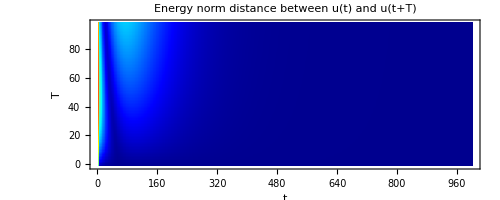

```mathematica
d  = f[f[f[Import[datdir <>"5\\rec\\rec1.csv"]]]];
d = d/Max[d];
scale = Table[{i,i},{i,0,Length[d[[1]]]-1,20}];
scale2 = Table[{Length[d]-1-i,i},{i,0,Length[d]-1,20}];
MatrixPlot[d,FrameTicks->{{scale2,None},{scale,None}},FrameLabel -> {Style["T",FontSize -> 20],Style["t",FontSize -> 20],None,None},PlotLabel -> Style["Energy norm distance between u(t) and u(t+T)",FontSize -> 20],ColorFunction ->Function[Blend[RGBColor@@@cMap,Slot[1]]],ColorFunctionScaling -> False,ImageSize->Full]
```

```mathematica
cMap=Partition[ToExpression[StringSplit[Import["C:\\Users\\Varchas\\Desktop\\Reed\\Thesis\\util\\mma\\colormap.txt"]]],3];
```

```mathematica
Length[d]
```

100